### 核関数の平滑化距離の変化の影響を確認する

```mathematica
ClearAll["Global`*"];
```

#### 関数の定義 （設定）

```mathematica
(*核関数の例*)
(*3次のBスプライン*)
wB3[r_,hin_]:=Module[{a,q,h},
h=hin/2;
a=1./(Pi*h^3);
q=r/h;
a*Piecewise[
{{1-3/2*q^2+3/4*q^3,0.≤q&&q≤ 1.},
{1/4*(2-q)^3,1.<q&&q≤2.}},
0.]
];
(*5次のBスプライン*)
wB5[r_,hin_]:=Module[{a,q,h},
h=hin/3;
a=1/(Pi*h^3)/120.;
q=r/h;
a*Piecewise[
{{(3-q)^5-6*(2-q)^5+15*(1-q)^5,0.≤q&&q≤ 1.},
{(3-q)^5-6*(2-q)^5,1.<q&&q≤2.},
{(3-q)^5,2.<q&&q≤3.}},
0.]
];
```

#### 積分計算する３点の座標を決める

```mathematica
dx=0.02;(*粒子の間隔*)
maxx=0.12;(*粒子の範囲*)
x=dx;y=dx;z=dx;
tmp=Table[x,{x,0,maxx,dx}]
```

{0.,0.02,0.04,0.06,0.08,0.1,0.12}

```mathematica
(*核関数による計算を行う3つの粒子の座標を適当に決める*)
P00={0,0,0};
P05={tmp[[Round[Length[tmp]/2+3]]],0,0};
P10={tmp[[Length[tmp]]],0,0};
```

#### ３点の周りに粒子を配置する

```mathematica
(*各粒子の座標*)
tab=ParallelTable[{x,y,z},{x,-maxx,maxx,dx},{y,-maxx,maxx,dx},{z,-maxx,maxx,dx}];
ps=Flatten[tab,2];
(*各粒子の持つ適当な値，全て1000としておく*)
values=Flatten[ParallelTable[1000,{x,-maxx,maxx,dx},{y,-maxx,maxx,dx},{z,-maxx,maxx,dx}],2];
```

```mathematica
Vol=(2maxx)^3;(*粒子を設定した領域全体の体積*)
n=(Dimensions[tab][[1]]-1);(*x方向の粒子の数-1*)
n*=(Dimensions[tab][[2]]-1)(*y方向の粒子の数-1*);
n*=(Dimensions[tab][[3]]-1)(*z方向の粒子の数-1*);
V=Vol/n;(*粒子一つが担う体積*)
radius=(V/(4/3*Pi))^(1/3);
edge=((4/3*Pi)^(1/3))*radius;

Print["粒子一つが持つべき半径",radius]
Print["粒子一つが担うべき立方体の一辺の長さ",edge]
Print["粒子一つが担う体積",V]

Show[
{ListPointPlot3D[ps],
Graphics3D[{PointSize[Large],Red,Point[P00]}],
Graphics3D[{PointSize[Large],Blue,Point[P05]}],
Graphics3D[{PointSize[Large],Green,Point[P10]}]
},
PlotRange->{{-maxx,maxx},{-maxx,maxx},{-maxx,maxx}},
BoxRatios->{1, 1, 1}
]
```

粒子一つが持つべき半径0.012407

粒子一つが担うべき立方体の一辺の長さ0.02

粒子一つが担う体積8.×10^-6

-Graphics3D-

#### ３点周りの粒子を使って，３点を中心に積分を計算し結果を確認

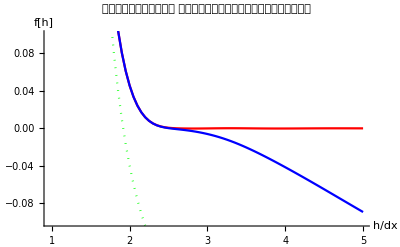

```mathematica
maxh=.1;(*プロットする最大の平滑化距離を設定*)
wB=wB5;(*核関数を選択設定*)

(*SUMの定義*)
F00[h_]:=Sum[values[[i]]*wB[Norm[ps[[i]]-P00],h]*V,{i,1,Length[ps],1}]
F05[h_]:=Sum[values[[i]]*wB[Norm[ps[[i]]-P05],h]*V,{i,1,Length[ps],1}]
F10[h_]:=Sum[values[[i]]*wB[Norm[ps[[i]]-P10],h]*V,{i,1,Length[ps],1}]
(*valuesを使って積分*)
tab00=ParallelTable[{h/dx,F00[h]},{h,0.01,maxh,maxh/100}];
tab05=ParallelTable[{h/dx,F05[h]},{h,0.01,maxh,maxh/100}];
tab10=ParallelTable[{h/dx,F10[h]},{h,0.01,maxh,maxh/100}];

(*プロットして確認*)
Show[
{ListPlot[{#1,#2/1000-1}&@@@tab00,Joined->True,PlotStyle->Red],
ListPlot[{#1,#2/1000-1}&@@@tab05,Joined->True,PlotStyle->Blue],
ListPlot[{#1,#2/1000-1}&@@@tab10,Joined->True,PlotStyle->{Green,Dotted}]}
,
PlotRange->{Automatic,{-.1,.1}},
PlotLabel->"領域の端に近い点では，\n粒子点が少なくなり，積分結果は小さくなる",
AxesLabel->{"h/dx","f[h]"}
]
```

#### この３点の積分で使われた平滑化距離内部の粒子数を確認してみる

```mathematica
(*平滑化距離内部の粒子数をカウントしてチェックしたいので，そのための関数を定義*)
Count00[h_]:=Sum[If[wB[Norm[ps[[i]]-P00],h]>10^-10,1,0],{i,1,Length[ps],1}]
Count05[h_]:=Sum[If[wB[Norm[ps[[i]]-P05],h]>10^-10,1,0],{i,1,Length[ps],1}]
Count10[h_]:=Sum[If[wB[Norm[ps[[i]]-P10],h]>10^-10,1,0],{i,1,Length[ps],1}]
(*平滑化距離内部の粒子数をカウントしてチェックしたい*)
tab00count=ParallelTable[{h/dx,Count00[h]},{h,0.01,maxh,maxh/500}];
tab05count=ParallelTable[{h/dx,Count05[h]},{h,0.01,maxh,maxh/500}];
tab10count=ParallelTable[{h/dx,Count10[h]},{h,0.01,maxh,maxh/500}];
```

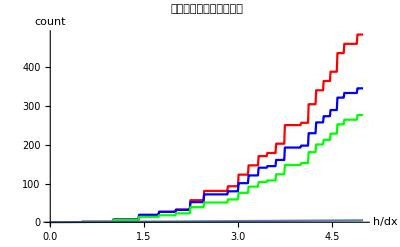

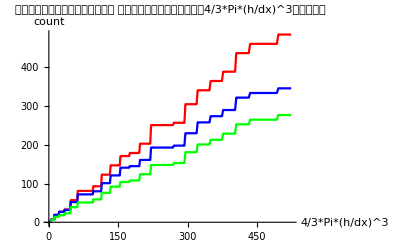

```mathematica
Show[
{ListPlot[tab00count,Joined->True,PlotStyle->Red],
ListPlot[tab05count,Joined->True,PlotStyle->Blue],
ListPlot[tab10count,Joined->True,PlotStyle->Green],
Plot[x,{x,0,5}]}
,
AxesLabel->{"h/dx","count"},
PlotLabel->"平滑化距離内部の粒子数"
]
Show[
{ListPlot[({4/3*Pi*#1^3,#2})&@@@tab00count,Joined->True,PlotStyle->Red],
ListPlot[({4/3*Pi*#1^3,#2})&@@@tab05count,Joined->True,PlotStyle->Blue],
ListPlot[({4/3*Pi*#1^3,#2})&@@@tab10count,Joined->True,PlotStyle->Green],
Plot[x,{x,0,5}]}
,
AxesLabel->{"4/3*Pi*(h/dx)^3","count"},
PlotLabel->"均等に配置せれていれば，当然，\n平滑化距離内部の粒子数は，4/3*Pi*(h/dx)^3に比例する"
]
```